```mathematica
(*Approximation de la probabilité de ruine ultime*)
(*Developpement de densité de probabilité bivariée*)
(*La mesure de référence choisi est la loi Gamma de paramètre ξ et ν*)
muGamma=Function[{x,m,r},(1/m)^(r)*Exp[-x/m]*x^(r-1)/Gamma[r]];
(*Polynôme mu orthogonaux associé*)
QnGamma=Function[{n,x,m,r},(-1)^n*LaguerreL[n,r-1,x/m]/Sqrt[Binomial[n+r-1,n]]];
(*Loi binomial negative de paramètre a et p*)
FoncGenPoisson=Function[{s,λ},Exp[λ(s-1)]-Exp[-λ]];
(*Distribution Gamma*)
LaplaceGamma=Function[{s,α,β},(1/(1-s*β))^(α)];
LaplaceCompoundPoissonGamma=Function[{s,λ,α,β},FoncGenPoisson[LaplaceGamma[s,α,β],λ]];
CoefGenFunctionCompoundPoissonGamma=Function[{λ,α,β,z,m,r},FullSimplify[(1+z)^(-r)*LaplaceCompoundPoissonGamma[z/m/(1+z),λ,α,β]]];
ExpansionCoefficientCompoundPoissonGamma=Function[{λ,α,β,z,m,r,K},Expansion=Normal[Series[CoefGenFunctionCompoundPoissonGamma[λ,α,β,z,m,r],{z,0,K}]];Table[1/Sqrt[Binomial[i+r-1,i]]/(i!)*(D[Expansion,{z,i}]/.z->0),{i,0,K}]];
(*Poisson coposée avec des sinistres de loi Gamma*)
NaiveDensityCompoundPoissonGamma=Function[{x,λ,α,β,KNaive},
Sum[Exp[-λ]*λ^(k)/k!*PDF[GammaDistribution[k*α,β],x],{k,1,KNaive}
]
];
NaiveSurvivalCompoundPoissonGamma=Function[{u,λ,α,β,KNaive},
Sum[Exp[-λ]*λ^(k)/k!*SurvivalFunction[GammaDistribution[k*α,β],u],{k,1,KNaive}]
];
(*Système de polynômes orthogonaux*)
Qnm=Function[{x,m,r,K},Table[QnGamma[i,x,m,r]muGamma[x,m,r],{i,0,K}]];
DensityExpansion=Function[{VectorCoef,x,m,r,K},Total[VectorCoef[[1;;K+1]]*Qnm[x,m,r,K]]];
SurvivalExpansion=Function[{VectorCoef,u,m,r,K},Integrate[DensityExpansion[VectorCoef,x,m,r,K],{x,u,+∞},Assumptions->Im[u]≠0||Re[u]>0]];
UsualStopLossPremiumExpansion=Function[{VectorCoef,c,m,r,K},
Integrate[SurvivalExpansion[VectorCoef,u+c,m,r,K]
,{u,0,+∞}]];
(*Evaluation de la probabilité de ruine via ls FFT*)
(*Fonction de sur£vie via les FFT*)
(*Calcul des Sn*)
FoncGenPoissonFFT=Function[{s,λ},Exp[λ(s-1)]];
LaplaceCompoundPoissonGammaSurvival=Function[{s,λ,α,β},(1-FoncGenPoissonFFT[LaplaceGamma[-s,α,β],λ])/s];
SnCompoundPoissonGammaSurvival=Function[{b,u,n,λ,α,β},Exp[b/2]/2/u*Re[LaplaceCompoundPoissonGammaSurvival[b/2/u,λ,α,β]]+Exp[b/2]/u*Sum[(-1)^(i)*Re[LaplaceCompoundPoissonGammaSurvival[(b+I*i*2π)/2/u,λ,α,β]],{i,1,n,1}]];
SurvivalCompoundPoissonGammaFFT=Function[{m,b,u,n,λ,α,β},Sum[Binomial[m,i]*2^(-m)SnCompoundPoissonGammaSurvival[b,u,n+i,λ,α,β],{i,0,m,1}]];
(*Evaluation de la probabilité de ruine via la scaled laplace Transform*)
LaplaceCompoundPoissonGammaMnats=Function[{s,λ,α,β},FoncGenPoissonFFT[LaplaceGamma[-s,α,β],λ]];
(*Formule de la densité et transformée de Laplace de la probabilité de ruine*)
SurvivalCompoundPoissonGammaMnats=Function[{λ,α,β,αMnats,bMnats,u},
Sum[
Sum[
Binomial[αMnats,j]*Binomial[j,k](-1)^(j-k)LaplaceCompoundPoissonGammaMnats[Log[bMnats]*j,λ,α,β]
,{j,k,αMnats}]
,{k,0,Floor[αMnats*Exp[-u*Log[bMnats]]]}
]];
DensityCompoundPoissonGammaMnats=Function[{λ,α,β,αMnats,bMnats,x},
Floor[αMnats*Exp[-Log[bMnats]*x]]Log[bMnats]Gamma[αMnats+2]/(αMnats*Gamma[Floor[αMnats*Exp[-Log[bMnats]*x]]+1])*
Sum[
(-1)^(j)*LaplaceCompoundPoissonGammaMnats[j+Floor[αMnats*Exp[-Log[bMnats]*x]],λ,α,β]/j!/(αMnats-Floor[αMnats*Exp[-Log[bMnats]*x]]-j)!
,{j,0,αMnats-Floor[αMnats*Exp[-Log[bMnats]*x]]}]
]
SurvivalCompoundPoissonGammaMnatsBis=Function[{λ,α,β,αMnats,bMnats,x},
Floor[αMnats*Exp[-Log[bMnats]*x]]Log[bMnats]Gamma[αMnats+2]/(αMnats*Gamma[Floor[αMnats*Exp[-Log[bMnats]*x]]+1])*
Sum[
(-1)^(j)*LaplaceCompoundPoissonGammaSurvival[j+Floor[αMnats*Exp[-Log[bMnats]*x]],λ,α,β]/j!/(αMnats-Floor[αMnats*Exp[-Log[bMnats]*x]]-j)!
,{j,0,αMnats-Floor[αMnats*Exp[-Log[bMnats]*x]]}]
]
(*Algorithme de Panjer*)
(*Discrétisation, h représente le pas de discrétisation, u est la limite, on créer un vecteur de taille u/h*)
DiscretizeGamma=Function[{α,β,umax,h},PartitionGrid=Table[k*h,{k,0,umax/h,1}];ProbaU=Table[N[CDF[GammaDistribution[α,β],Max[PartitionGrid[[i]]+h/2,0]]-CDF[GammaDistribution[α,β],Max[PartitionGrid[[i]]-h/2,0]]],{i,1,Length[PartitionGrid](*-1*),1}]];
ProbaDiscretePoissonCompoundGamma=Function[{λ,h,VectProbaU,umax},ProbaCompoundPoisson={};AppendTo[ProbaCompoundPoisson,Exp[-λ]];
For[j=1,j<umax/h+1,j++,AppendTo[ProbaCompoundPoisson,Sum[λ*k/j*VectProbaU[[k]]*ProbaCompoundPoisson[[(j-k)+1]],{k,1,j,1}]]];ProbaCompoundPoisson];
SurvivalPoissonCompoundGammaPanger=Function[{VectProbaCompoundPoisson,h,u},1-Sum[VectProbaCompoundPoisson[[k]],{k,1,u/h}]];
StopLossPremiumCompoundPoissonGammaPanjer=Function[{VectSurvivalCompoundPoisson,h,u,λ,α,β},λ*α*β-Sum[]];
```

Function[{λ,α,β,αMnats,bMnats,x},(Floor[αMnats Exp[-Log[bMnats] x]] Log[bMnats] Gamma[αMnats+2] ∑_(j=0)^(αMnats-Floor[αMnats Exp[-Log[bMnats] x]]) ((-1)^j LaplaceCompoundPoissonGammaMnats[j+Floor[αMnats Exp[-Log[bMnats] x]],λ,α,β])/(j! (αMnats-Floor[αMnats Exp[-Log[bMnats] x]]-j)!))/(αMnats Gamma[Floor[αMnats Exp[-Log[bMnats] x]]+1])]

Function[{λ,α,β,αMnats,bMnats,x},(Floor[αMnats Exp[-Log[bMnats] x]] Log[bMnats] Gamma[αMnats+2] ∑_(j=0)^(αMnats-Floor[αMnats Exp[-Log[bMnats] x]]) ((-1)^j LaplaceCompoundPoissonGammaSurvival[j+Floor[αMnats Exp[-Log[bMnats] x]],λ,α,β])/(j! (αMnats-Floor[αMnats Exp[-Log[bMnats] x]]-j)!))/(αMnats Gamma[Floor[αMnats Exp[-Log[bMnats] x]]+1])]

```mathematica
(*Sinistres de loi gamma*)
α=3;
β=1;
(*Fréquence des sinistres de loi de Poisson*)
λ=2;
μ=λ*Mean[GammaDistribution[α,β]];
Var=λ*Mean[GammaDistribution[α,β]]+Moment[GammaDistribution[α,β],2]*λ;
(*Coefficient de la représentation polynomiale*)
NbParametrization=4;
m={β,β,μ,Var/μ}
r={α,1,1,N[μ^(2)/Var]}
(*Fonction génératrice des coefficients*)
(*Table[CoefGenFunctionCompoundPoissonGamma[λ,α,β,z,m[[i]],r[[i]]],{i,1,NbParametrization}]*)
```

{1,1,6,5}

{3,1,1,1.2}

```mathematica
(*Coefficients et polynômes orthogonaux*)
KPoly=85;
MatrixForm[N[VectorCoef=Table[ExpansionCoefficientCompoundPoissonGamma[λ,α,β,z,m[[i]],r[[i]],KPoly],{i,1,NbParametrization}]]]
(*Matrice des polynomes multipliés par leur mesure*)
(*Approximation de la densité*)
MatrixForm[SurvivalCompoundPoissonGammaPolynomial=Table[SurvivalExpansion[VectorCoef[[i]],u,m[[i]],r[[i]],KPoly],{i,1,NbParametrization}]];
MatrixForm[DensityCompoundPoissonGammaPolynomial=Table[DensityExpansion[VectorCoef[[i]],x,m[[i]],r[[i]],KPoly],{i,1,NbParametrization}]];
```

(0.864665 | 1.96646 | 4.56748 | 9.28235 | 17.2916 | 29.8177 | 48.1169 | 73.2692 | 105.951 | 146.26 | 193.572 | 246.5 | 302.948 | 360.271 | 415.513 | 465.689 | 508.067 | 540.423 | 561.227 | 569.74 | 566.03 | 550.897 | 525.747 | 492.413 | 452.971 | 409.557 | 364.21 | 318.753 | 274.708 | 233.258 | 195.241 | 161.168 | 131.265 | 105.527 | 83.7716 | 65.6907 | 50.9024 | 38.9891 | 29.5294 | 22.1208 | 16.3947 | 12.0249 | 8.73062 | 6.27623 | 4.46832 | 3.15122 | 2.20188 | 1.52468 | 1.04644 | 0.712011 | 0.480365 | 0.321398 | 0.213292 | 0.140422 | 0.0917258 | 0.0594574 | 0.038251 | 0.0244264 | 0.0154851 | 0.00974687 | 0.00609204 | 0.00378147 | 0.00233135 | 0.00142776 | 0.000868656 | 0.000525088 | 0.000315393 | 0.000188257 | 0.000111679 | 0.0000658492 | 0.000038595 | 0.0000224879 | 0.000013027 | 7.50322×10^-6 | 4.29734×10^-6 | 2.44755×10^-6 | 1.38636×10^-6 | 7.8103×10^-7 | 4.3766×10^-7 | 2.43957×10^-7 | 1.35278×10^-7 | 7.46293×10^-8 | 4.09625×10^-8 | 2.2371×10^-8 | 1.21573×10^-8 | 6.57451×10^-9
0.864665 | 5.13534 | 18.8647 | 55.1353 | 136.865 | 299.935 | 594.865 | 1085.48 | 1844.58 | 2945.78 | 4452.71 | 6406.89 | 8816.58 | 11648.6 | 14825. | 18225.9 | 21697.8 | 25066.6 | 28154.3 | 30795.2 | 32851.5 | 34224.7 | 34862.4 | 34760.1 | 33958.1 | 32534. | 30593.2 | 28257.8 | 25655.9 | 22911.6 | 20137.6 | 17429.7 | 14864. | 12495.6 | 10359.9 | 8474.67 | 6842.84 | 5455.88 | 4297.01 | 3344.2 | 2572.66 | 1956.92 | 1472.29 | 1095.88 | 807.235 | 588.589 | 424.919 | 303.796 | 215.148 | 150.96 | 104.965 | 72.339 | 49.4222 | 33.4791 | 22.4907 | 14.9857 | 9.9054 | 6.49605 | 4.22741 | 2.7303 | 1.75031 | 1.1139 | 0.703821 | 0.441585 | 0.27514 | 0.170268 | 0.104665 | 0.063915 | 0.038778 | 0.0233773 | 0.0140046 | 0.00833787 | 0.00493391 | 0.00290213 | 0.00169695 | 0.000986481 | 0.000570175 | 0.000327691 | 0.00018728 | 0.000106444 | 0.0000601709 | 0.0000338314 | 0.0000189214 | 0.0000105272 | 5.82682×10^-6 | 3.20875×10^-6
0.864665 | 0.135335 | -0.302002 | 0.227928 | -0.126076 | 0.054934 | -0.0179656 | 0.00416367 | -0.00244419 | 0.00531966 | -0.00875904 | 0.0110861 | -0.0119387 | 0.0115501 | -0.0103331 | 0.00867857 | -0.00688146 | 0.00513232 | -0.00353599 | 0.00213711 | -0.0009431 | -0.0000587015 | 0.000889613 | -0.00157288 | 0.00213023 | -0.00258044 | 0.00293915 | -0.00321916 | 0.00343099 | -0.00358342 | 0.00368392 | -0.00373902 | 0.00375453 | -0.00373574 | 0.00368746 | -0.00361412 | 0.00351978 | -0.00340817 | 0.00328266 | -0.00314631 | 0.00300188 | -0.0028518 | 0.00269824 | -0.00254309 | 0.00238798 | -0.00223432 | 0.0020833 | -0.00193592 | 0.00179298 | -0.00165515 | 0.00152293 | -0.00139672 | 0.00127679 | -0.0011633 | 0.00105635 | -0.00095595 | 0.000862048 | -0.000774541 | 0.000693279 | -0.000618076 | 0.000548717 | -0.000484964 | 0.00042656 | -0.000373238 | 0.000324722 | -0.000280731 | 0.000240985 | -0.000205205 | 0.000173117 | -0.000144455 | 0.000118958 | -0.0000963756 | 0.0000764694 | -0.0000590105 | 0.0000437822 | -0.0000305798 | 0.0000192107 | -9.49464×10^-6 | 1.26342×10^-6 | 5.63936×10^-6 | -0.0000113585 | 0.0000160275 | -0.0000197692 | 0.0000226961 | -0.0000249108 | 0.0000265067
0.864665 | 0.148252 | -0.259935 | 0.160588 | -0.0698084 | 0.0238093 | -0.0094274 | 0.0095268 | -0.0134412 | 0.0164985 | -0.0175037 | 0.0167555 | -0.0149435 | 0.0126779 | -0.010362 | 0.00821088 | -0.00631039 | 0.00467374 | -0.00328054 | 0.00209976 | -0.00110086 | 0.000257901 | 0.000449895 | -0.00103908 | 0.00152317 | -0.00191368 | 0.00222084 | -0.00245406 | 0.00262211 | -0.00273319 | 0.00279502 | -0.00281474 | 0.00279892 | -0.00275358 | 0.00268414 | -0.00259545 | 0.00249182 | -0.00237704 | 0.0022544 | -0.00212674 | 0.00199649 | -0.00186569 | 0.00173607 | -0.00160901 | 0.00148564 | -0.00136685 | 0.00125331 | -0.0011455 | 0.00104376 | -0.000948272 | 0.000859119 | -0.000776281 | 0.00069966 | -0.000629096 | 0.000564377 | -0.000505252 | 0.000451443 | -0.000402651 | 0.000358567 | -0.000318874 | 0.000283257 | -0.000251404 | 0.00022301 | -0.00019778 | 0.000175434 | -0.000155703 | 0.000138334 | -0.000123092 | 0.000109755 | -0.0000981197 | 0.0000879966 | -0.0000792132 | 0.0000716118 | -0.0000650492 | 0.0000593956 | -0.0000545344 | 0.0000503609 | -0.0000467817 | 0.0000437137 | -0.0000410836 | 0.0000388266 | -0.000036886 | 0.0000352121 | -0.0000337619 | 0.0000324983 | -0.0000313893)

```mathematica
UsualStopLossCompoundPoissonGammaPolynomial=Integrate[SurvivalCompoundPoissonGammaPolynomial[[1]]/.u->y+c,{y,0,+∞}];
```

```mathematica
(*Application de l'algoo de Panjer*)
h=1/100;
umax=30;
VectProbaU=DiscretizeGamma[α,β,umax,h];
VectProbaCompoundPoisson=ProbaDiscretePoissonCompoundGamma[λ,h,VectProbaU,umax];
```

```mathematica
(*Survival Function Via Inversion of Fourier*)
bFFT=18.5;
mFFT=11;
nFFT=15;
uFFT=30;
(*Paramétrisation Mnatskanov*)
αMnats=32;
bMnats=1.115;
(*Comparaison des valeurs*)
(*N[SurvivalCompoundPoissonGammaMnats[λ,α,β,αMnats,bMnats,uFFT]]
SurvivalCompoundPoissonGammaFFT[mFFT,bFFT,uFFT,nFFT,λ,α,β]
Table[N[SurvivalCompoundPoissonGammaPolynomial[[i]]/.u->uFFT],{i,1,NbParametrization}]
SurvivalPoissonCompoundGammaPanger[VectProbaCompoundPoisson,h,uFFT]*)
```

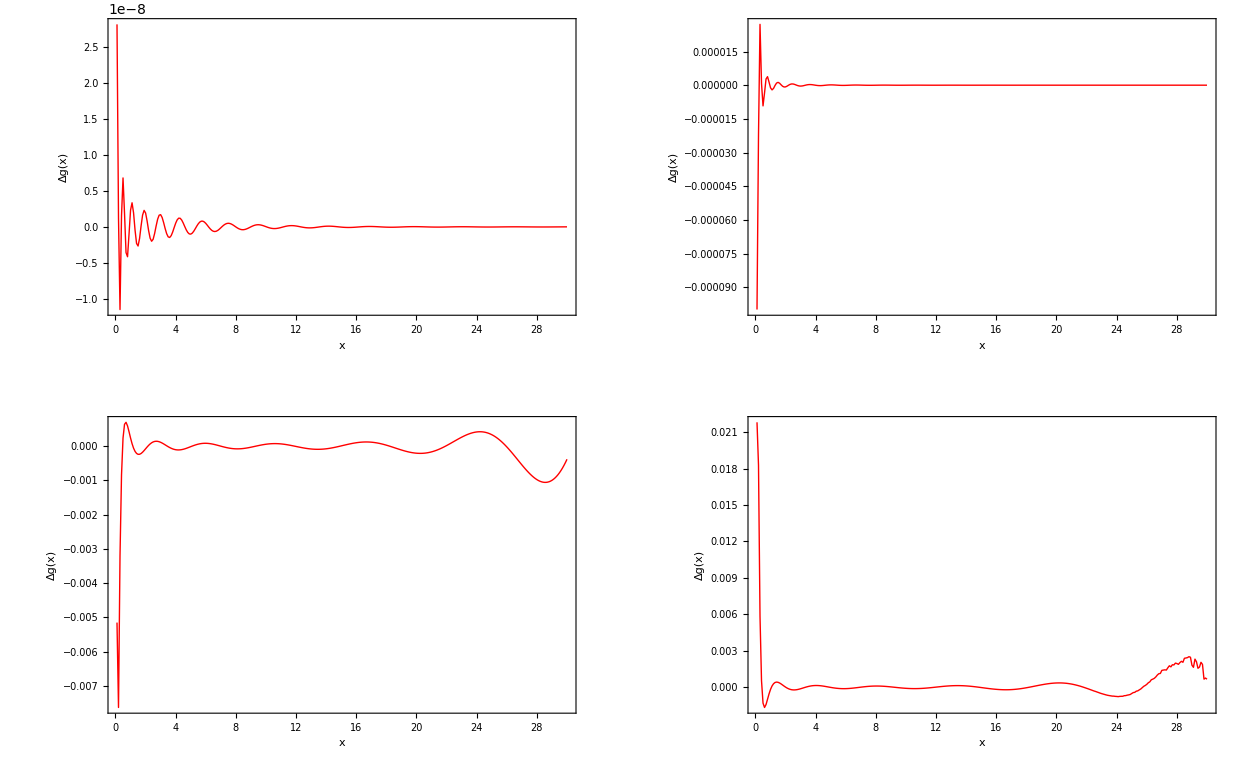

```mathematica
(*Fonction de survie pour différente paramétrisations comparaison avec Fourier*)
(*Graph D'erreur relative Pour différentes paramétrisations*)
(*Densité de probabilité*)
GraphicsGrid[{{DiscretePlot[(DensityCompoundPoissonGammaPolynomial[[1]]-NaiveDensityCompoundPoissonGamma[x,λ,α,β,50])/NaiveDensityCompoundPoissonGamma[x,λ,α,β,50],{x,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["Δg(x)",24],None},{Style["x",24],Style["Parametrization 1",24]}},ImageSize->Large,PlotStyle->Red],DiscretePlot[(DensityCompoundPoissonGammaPolynomial[[2]]-NaiveDensityCompoundPoissonGamma[x,λ,α,β,50])/NaiveDensityCompoundPoissonGamma[x,λ,α,β,50],{x,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["Δg(x)",24],None},{Style["x",24],Style["Parametrization 2",24]}},ImageSize->Large,PlotStyle->Red]
},
{DiscretePlot[(DensityCompoundPoissonGammaPolynomial[[3]]-NaiveDensityCompoundPoissonGamma[x,λ,α,β,50])/NaiveDensityCompoundPoissonGamma[x,λ,α,β,50],{x,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Joined->True,Filling->None,Frame->True,FrameLabel->{{Style["Δg(x)",24],None},{Style["x",24],Style["Parametrization 3",24]}},ImageSize->Large,PlotStyle->Red],
DiscretePlot[(DensityCompoundPoissonGammaPolynomial[[4]]-NaiveDensityCompoundPoissonGamma[x,λ,α,β,50])/NaiveDensityCompoundPoissonGamma[x,λ,α,β,50],{x,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["Δg(x)",24],None},{Style["x",24],Style["Parametrization 4",24]}},ImageSize->Large,PlotStyle->Red]
}
}]
```

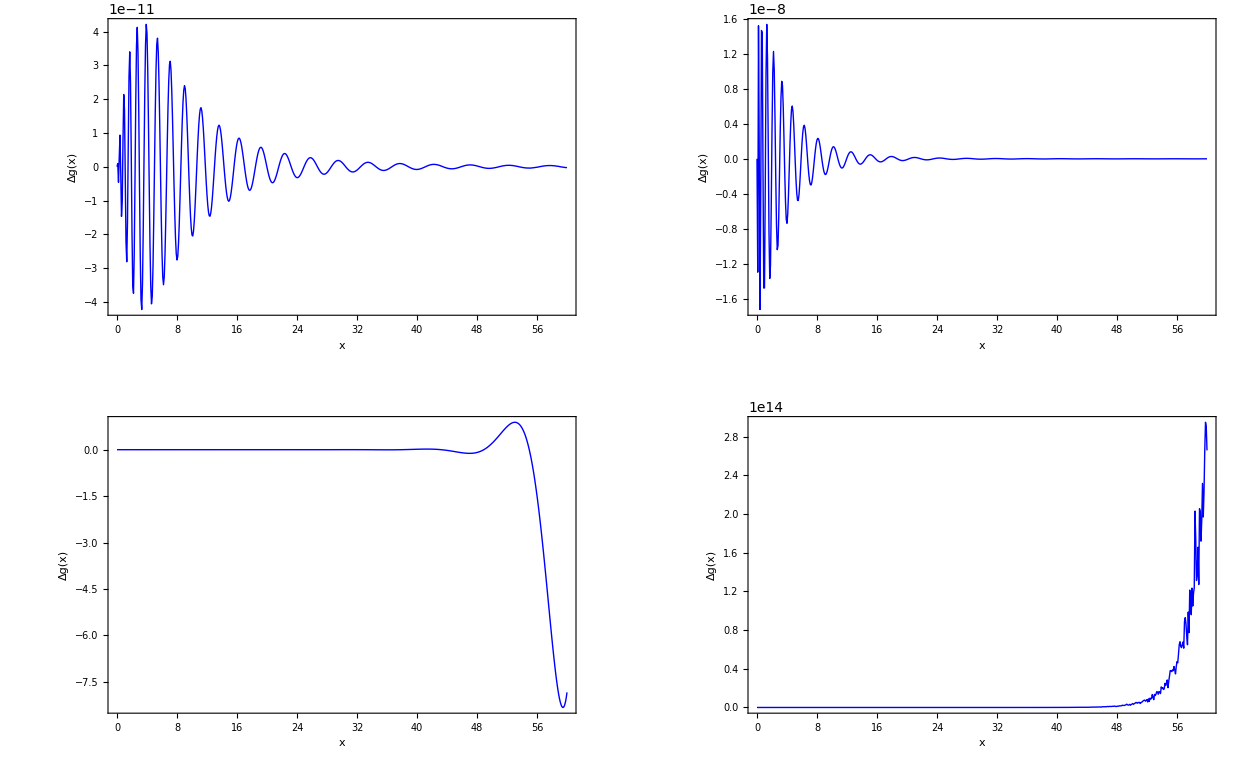

```mathematica
(*Fonction de survie de probabilité*)
GraphicsGrid[{{DiscretePlot[(SurvivalCompoundPoissonGammaPolynomial[[1]]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["Δg(x)",24],None},{Style["x",24],Style["Parametrization 1",24]}},ImageSize->Large,PlotStyle->Blue],DiscretePlot[(SurvivalCompoundPoissonGammaPolynomial[[2]]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["Δg(x)",24],None},{Style["x",24],Style["Parametrization 2",24]}},ImageSize->Large,PlotStyle->Blue]
},
{DiscretePlot[(SurvivalCompoundPoissonGammaPolynomial[[3]]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["Δg(x)",24],None},{Style["x",24],Style["Parametrization 3",24]}},ImageSize->Large,PlotStyle->Blue],
DiscretePlot[(SurvivalCompoundPoissonGammaPolynomial[[4]]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["Δg(x)",24],None},{Style["x",24],Style["Parametrization 4",24]}},ImageSize->Large,PlotStyle->Blue]
}
}]
```

```mathematica
(*Tableau fonction de survie et erreur relative sur la fonction de survie pour différentes paramétrisation du développement polynomiale*)
(*Fonction de survie*)
TeXForm[Table[{N[k],N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]],N[SurvivalCompoundPoissonGammaPolynomial[[1]]/.u->k],N[SurvivalCompoundPoissonGammaPolynomial[[2]]/.u->k],N[SurvivalCompoundPoissonGammaPolynomial[[3]]/.u->k],N[SurvivalCompoundPoissonGammaPolynomial[[4]]/.u->k]},{k,umax/10,umax,umax/10}]]
```

\left(
\begin{array}{cccccc}
 3. & 0.685132 & 0.685132 & 0.685132 & 0.685129684405966 & -196608. \\
 6. & 0.4313 & 0.4313 & 0.4313 & 0.4312998075851672 & -196608. \\
 9. & 0.238763 & 0.238763 & 0.238763 & 0.2387659551114337 & -196608. \\
 12. & 0.118895 & 0.118895 & 0.118895 & 0.1188930633146204 & -196608. \\
 15. & 0.0542376 & 0.0542376 & 0.0542376 & 0.0542391347023080 & -196608. \\
 18. & 0.0229767 & 0.0229767 & 0.0229767 & 0.02297562688304532 & -196608. \\
 21. & 0.00913388 & 0.00913388 & 0.00913388 & 0.00913441062425491 & -196608. \\
 24. & 0.00343513 & 0.00343513 & 0.00343513 & 0.003435161973479350 & -196608. \\
 27. & 0.00123021 & 0.00123021 & 0.00123021 & 0.001229840015775124 & -196608. \\
 30. & 0.000421752 & 0.000421752 & 0.000421752 & 0.000422070029215839 & -196608. \\
\end{array}
\right)

```mathematica
(*Erreur relative*)
TeXForm[Table[{N[k],N[Round[(N[SurvivalCompoundPoissonGammaPolynomial[[1]]/.u->k]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5],N[Round[(N[SurvivalCompoundPoissonGammaPolynomial[[2]]/.u->k]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5],N[Round[(N[SurvivalCompoundPoissonGammaPolynomial[[3]]/.u->k]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5],
N[Round[(N[SurvivalCompoundPoissonGammaPolynomial[[4]]/.u->k]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5]
},{k,umax/10,umax,umax/10}]]
```

\left(
\begin{array}{ccccc}
 3. & 0. & 0. & -0.0004 & -2.86965\times 10^7 \\
 6. & 0. & 0. & 0.00006 & -4.55851\times 10^7 \\
 9. & 0. & 0. & 0.00111 & -8.23444\times 10^7 \\
 12. & 0. & 0. & -0.00181 & -1.65363\times 10^8 \\
 15. & 0. & 0. & 0.00287 & -3.62494\times 10^8 \\
 18. & 0. & 0. & -0.00469 & -8.55684\times 10^8 \\
 21. & 0. & 0. & 0.00586 & -2.15251\times 10^9 \\
 24. & 0. & 0. & 0.0008 & -5.72344\times 10^9 \\
 27. & 0. & 0. & -0.03009 & -1.59817\times 10^{10} \\
 30. & 0. & 0. & 0.07546 & -4.6617\times 10^{10} \\
\end{array}
\right)

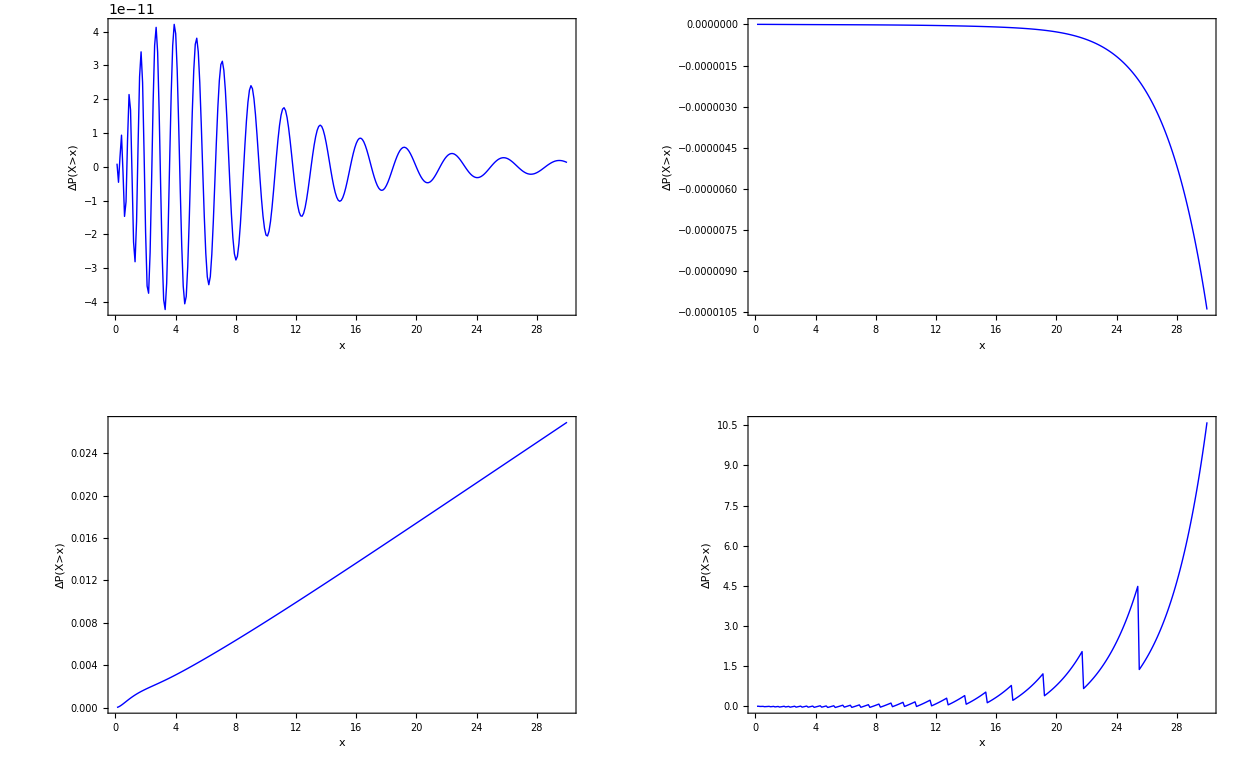

```mathematica
(*Erreur relative sur la fonction de survie avec différentes Méthodes*)
GraphicsGrid[{
{DiscretePlot[(SurvivalCompoundPoissonGammaPolynomial[[1]]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Polynomial",24]}},ImageSize->Large,PlotStyle->Blue],
DiscretePlot[(SurvivalCompoundPoissonGammaFFT[mFFT,bFFT,u,nFFT,λ,α,β]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Fourier",24]}},ImageSize->Large,PlotStyle->Blue]
},
{DiscretePlot[(SurvivalPoissonCompoundGammaPanger[VectProbaCompoundPoisson,h,u]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Panjer",24]}},ImageSize->Large,PlotStyle->Blue],DiscretePlot[(SurvivalCompoundPoissonGammaMnats[λ,α,β,αMnats,bMnats,u]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Exponential Moments",24]}},ImageSize->Large,PlotStyle->Blue]}}]
```

```mathematica
(*Tableau fonction de survie et erreur relative sur la fonction de survie*)
TeXForm[Table[{N[k],N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]],N[SurvivalCompoundPoissonGammaPolynomial[[1]]/.u->k],N[SurvivalCompoundPoissonGammaFFT[mFFT,bFFT,k,nFFT,λ,α,β]],N[SurvivalCompoundPoissonGammaMnats[λ,α,β,αMnats,bMnats,k]],N[SurvivalPoissonCompoundGammaPanger[VectProbaCompoundPoisson,h,k]]},{k,3,30,3}]]
```

\left(
\begin{array}{cccccc}
 3. & 0.685132 & 0.685132 & 0.685132 & 0.685203 & 0.686771 \\
 6. & 0.4313 & 0.4313 & 0.4313 & 0.422254 & 0.433313 \\
 9. & 0.238763 & 0.238763 & 0.238763 & 0.266124 & 0.24049 \\
 12. & 0.118895 & 0.118895 & 0.118895 & 0.129356 & 0.120076 \\
 15. & 0.0542376 & 0.0542376 & 0.0542376 & 0.076121 & 0.0549268 \\
 18. & 0.0229767 & 0.0229767 & 0.0229767 & 0.0364145 & 0.0233334 \\
 21. & 0.00913388 & 0.00913388 & 0.00913387 & 0.0222035 & 0.00930159 \\
 24. & 0.00343513 & 0.00343513 & 0.00343513 & 0.011718 & 0.003508 \\
 27. & 0.00123021 & 0.00123021 & 0.00123021 & 0.00489717 & 0.00125982 \\
 30. & 0.000421752 & 0.000421752 & 0.000421747 & 0.00489717 & 0.000433105 \\
\end{array}
\right)

```mathematica
TeXForm[Table[{N[k],
N[Round[(N[SurvivalCompoundPoissonGammaPolynomial[[1]]/.u->k]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5],N[Round[(N[SurvivalCompoundPoissonGammaFFT[mFFT,bFFT,k,nFFT,λ,α,β]]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5],N[Round[(N[SurvivalCompoundPoissonGammaMnats[λ,α,β,αMnats,bMnats,k]]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5],N[Round[(N[SurvivalPoissonCompoundGammaPanger[VectProbaCompoundPoisson,h,k]]-N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]])/N[NaiveSurvivalCompoundPoissonGamma[k,λ,α,β,50]]*100*10^5]*10^-5]},{k,3,30,3}]]
```

\left(
\begin{array}{ccccc}
 3. & 0. & 0. & 0.01036 & 0.2392 \\
 6. & 0. & 0. & -2.0972 & 0.46687 \\
 9. & 0. & 0. & 11.4594 & 0.72337 \\
 12. & 0. & 0. & 8.79806 & 0.99333 \\
 15. & 0. & -0.00001 & 40.3474 & 1.27079 \\
 18. & 0. & -0.00001 & 58.4844 & 1.55239 \\
 21. & 0. & -0.00004 & 143.089 & 1.83622 \\
 24. & 0. & -0.00012 & 241.122 & 2.12116 \\
 27. & 0. & -0.00036 & 298.076 & 2.40651 \\
 30. & 0. & -0.00104 & 1061.15 & 2.69184 \\
\end{array}
\right)

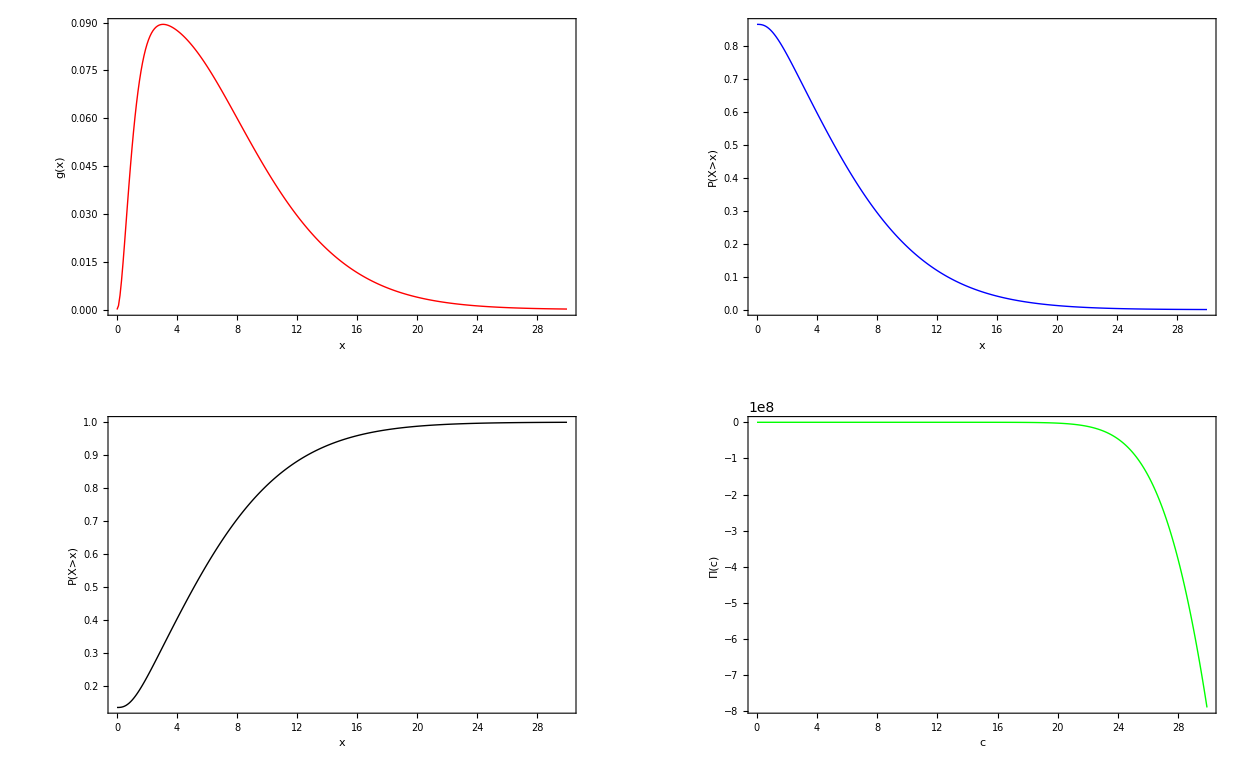

```mathematica
(*Approximation polynomiale de la densité défaillante, de la fonction de survie et de la prime stop-loss*)
GraphicsGrid[{{
DiscretePlot[DensityCompoundPoissonGammaPolynomial[[1]],{x,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,Filling->None,FrameLabel->{{Style["g(x)",24],None},{Style["x",24],Style["PDF",24]}},ImageSize->Large,PlotStyle->{Red,Thick}],
DiscretePlot[SurvivalCompoundPoissonGammaPolynomial[[1]],{u,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Filling->None,Joined->True,Filling->None,FrameLabel->{{Style["P(X>x)",24],None},{Style["x",24],Style["Survival Function",24]}},ImageSize->Large,PlotStyle->{Blue,Thick}]},
{DiscretePlot[1-SurvivalCompoundPoissonGammaPolynomial[[1]],{u,0,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Filling->None,Joined->True,Filling->None,FrameLabel->{{Style["P(X>x)",24],None},{Style["x",24],Style["Survival Function",24]}},ImageSize->Large,PlotStyle->{Black,Thick}],
DiscretePlot[UsualStopLossCompoundPoissonGammaPolynomial,{c,1/100,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["Π(c)",24],None},{Style["c",24],Style["Usual Stop Loss Premium",24]}},ImageSize->Large,PlotStyle->{Green,Thick}]}}]
```

```mathematica
(*Stop Loss Premium par simulations*)
NObs=1000000;
SamplePoisson=RandomVariate[PoissonDistribution[λ],NObs];
SampleCompoundPoissonGamma=Table[Total[RandomVariate[GammaDistribution[α,β],SamplePoisson[[i]]]],{i,1,NObs,1}];
```

```mathematica
TeXForm[Table[{Retention,Mean[Table[Max[SampleCompoundPoissonGamma[[i]]-Retention,0],{i,1,NObs,1}]],N[UsualStopLossCompoundPoissonGammaPolynomial/.c->Retention],((N[UsualStopLossCompoundPoissonGammaPolynomial/.c->Retention]-Mean[Table[Max[SampleCompoundPoissonGamma[[i]]-Retention,0],{i,1,NObs,1}]])/Mean[Table[Max[SampleCompoundPoissonGamma[[i]]-Retention,0]  ,{i,1,NObs,1}]])*100},{Retention,0,umax,umax/10}]]
```

\left(
\begin{array}{cccc}
 0 & 5.99316 & 6. & 0.114172 \\
 3 & 3.59554 & 3.60192 & 0.177357 \\
 6 & 1.93243 & 1.9526 & 1.04382 \\
 9 & 0.94746 & 29.3862 & 3001.58 \\
 12 & 0.429122 & 834.273 & 194314. \\
 15 & 0.181003 & -14846.1 & -8.2022\times 10^6 \\
 18 & 0.0716428 & -415589. & -5.80085\times 10^8 \\
 21 & 0.0269423 & -5.36322\times 10^6 & -1.99063\times 10^{10} \\
 24 & 0.00976161 & -4.62574\times 10^7 & -4.7387\times 10^{11} \\
 27 & 0.00342669 & -2.43286\times 10^8 & -7.09975\times 10^{12} \\
 30 & 0.00113488 & -8.13887\times 10^8 & -7.17157\times 10^{13} \\
\end{array}
\right)

```mathematica
(*Comparaison Monte Carlo/ Polynome*)
(*Computation time trial*)
(*Sinistres de loi gamma*)
α=3;
β=1;
(*Fréquence des sinistres de loi de Poisson*)
λ=2;
μ=λ*Mean[GammaDistribution[α,β]];
Var=λ*Mean[GammaDistribution[α,β]]+Moment[GammaDistribution[α,β],2]*λ;
(*Coefficient de la représentation polynomiale*)
NbParametrization=1;
m={β,β,μ,Var/μ}
r={α,1,1,N[μ^(2)/Var]}
```

{1,1,6,5}

{3,1,1,1.2}

```mathematica
(*Coefficients et polynômes orthogonaux*)
KPoly=75;
Timing[MatrixForm[N[VectorCoef=Table[ExpansionCoefficientCompoundPoissonGamma[λ,α,β,z,m[[i]],r[[i]],KPoly],{i,1,NbParametrization}]]]]
(*Matrice des polynomes multipliés par leur mesure*)
(*Approximation de la densité*)
Timing[MatrixForm[SurvivalCompoundPoissonGammaPolynomial=Table[SurvivalExpansion[VectorCoef[[i]],u,m[[i]],r[[i]],KPoly],{i,1,NbParametrization}]]][[1]]
```

{2.29412,(0.864665 | 1.96646 | 4.56748 | 9.28235 | 17.2916 | 29.8177 | 48.1169 | 73.2692 | 105.951 | 146.26 | 193.572 | 246.5 | 302.948 | 360.271 | 415.513 | 465.689 | 508.067 | 540.423 | 561.227 | 569.74 | 566.03 | 550.897 | 525.747 | 492.413 | 452.971 | 409.557 | 364.21 | 318.753 | 274.708 | 233.258 | 195.241 | 161.168 | 131.265 | 105.527 | 83.7716 | 65.6907 | 50.9024 | 38.9891 | 29.5294 | 22.1208 | 16.3947 | 12.0249 | 8.73062 | 6.27623 | 4.46832 | 3.15122 | 2.20188 | 1.52468 | 1.04644 | 0.712011 | 0.480365 | 0.321398 | 0.213292 | 0.140422 | 0.0917258 | 0.0594574 | 0.038251 | 0.0244264 | 0.0154851 | 0.00974687 | 0.00609204 | 0.00378147 | 0.00233135 | 0.00142776 | 0.000868656 | 0.000525088 | 0.000315393 | 0.000188257 | 0.000111679 | 0.0000658492 | 0.000038595 | 0.0000224879 | 0.000013027 | 7.50322×10^-6 | 4.29734×10^-6 | 2.44755×10^-6)}

18.0506

```mathematica
(*Echantillon*)
NObs=Table[l,{l,100000,1000000,100000}];
TimeU={};TimeX={};TimeDistX={};
For[k=1,k<Length[NObs]+1,k++,EchN=RandomVariate[PoissonDistribution[λ],NObs[[k]]];AppendTo[TimeU,Timing[EchU=Table[RandomVariate[GammaDistribution[α,β],EchN[[i]]],{i,1,NObs[[k]]}]][[1]]];
AppendTo[TimeX,Timing[EchX=Table[Total[EchU[[i]]],{i,1,NObs[[k]],1}]][[1]]];
AppendTo[TimeDistX,Timing[DistX=EmpiricalDistribution[EchX]][[1]]];
]
TimeU
TimeX
TimeDistX
```

{2.3396,4.47837,6.68433,8.97421,11.2773,13.48241,15.96142,17.82625,19.83117,22.28345}

{1.03004,2.26777,3.38655,4.70756,6.08808,7.50372,9.17922,10.48198,12.6912,13.83406}

{0.19205,0.27745,0.43309,0.67418,0.88863,1.15571,1.43948,1.69174,2.07689,2.42345}

```mathematica
TimeMC=Table[TimeU[[j]]+TimeX[[j]]+TimeDistX[[j]],{j,1,Length[NObs]}]
TimePolynomial=Table[20,{j,1,Length[NObs]}]
```

{3.56169,7.02358,10.504,14.356,18.254,22.1418,26.5801,29.99996,34.59927,38.54096}

{20,20,20,20,20,20,20,20,20,20}

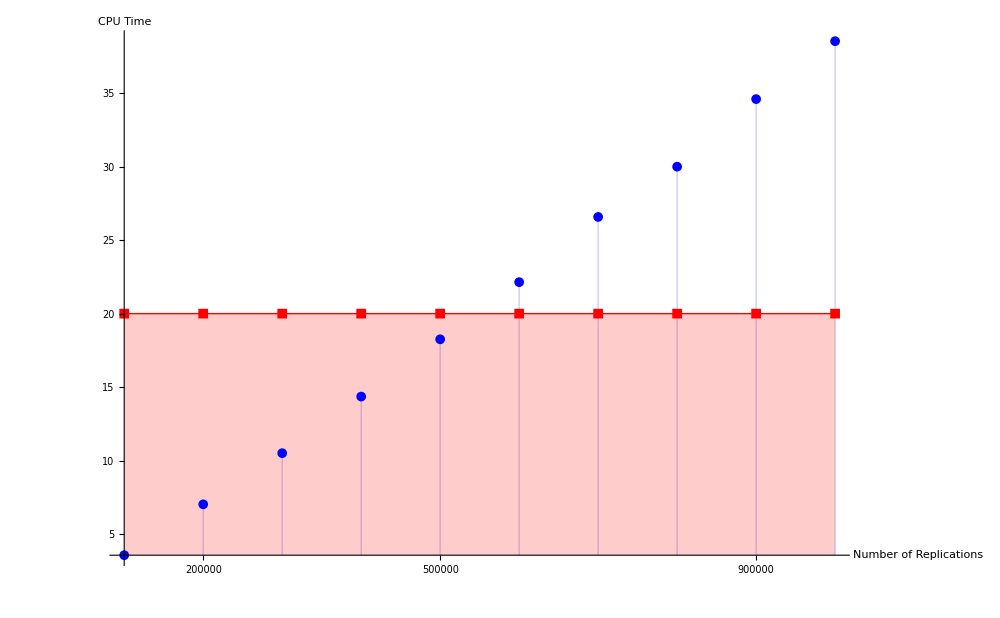

```mathematica
DiscretePlot[{TimeMC[[j/100000]],TimePolynomial[[j/100000]]},{j,100000,1000000,100000},LabelStyle->Directive[Black,24],ImageSize->1000,PlotStyle->{Blue,Red},Joined->{False,True},PlotMarkers->{Automatic,Automatic},AxesLabel->{"Number of Replications","CPU Time"},PlotRange->All,Ticks->{{2*10^(5),5*10^(5),9*10^(5)},Automatic}]
```

```mathematica
(*Echantillon*)
NObs=600000;

EchN=RandomVariate[PoissonDistribution[λ],NObs];
EchU=Table[RandomVariate[GammaDistribution[α,β],EchN[[i]]],{i,1,NObs}];
EchX=Table[Total[EchU[[i]]],{i,1,NObs,1}];
DistX=EmpiricalDistribution[EchX];
```

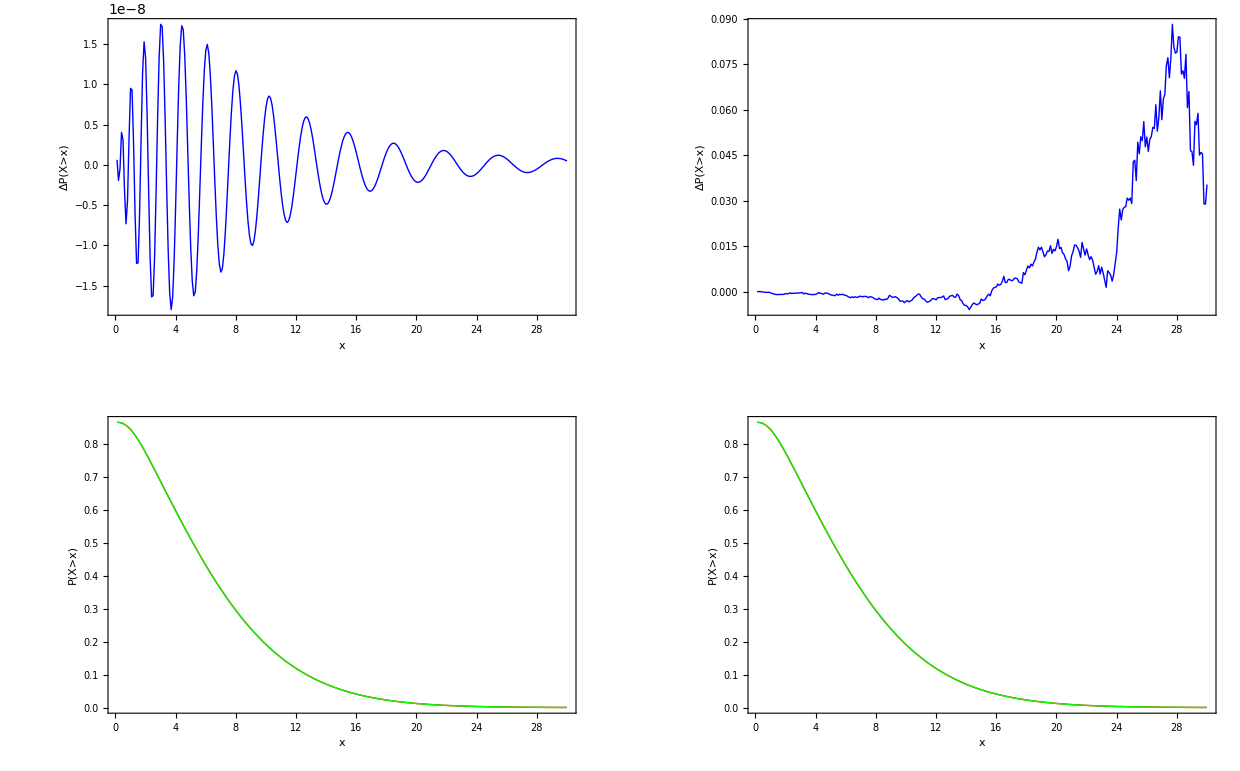

```mathematica
umax=30;
GraphicsGrid[
{{DiscretePlot[(SurvivalCompoundPoissonGammaPolynomial[[1]]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Polynomial",24]}},ImageSize->Large,PlotStyle->Blue],
DiscretePlot[(SurvivalFunction[DistX,u]-NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50])/NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50],{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["ΔP(X>x)",24],None},{Style["x",24],Style["Monte Carlo",24]}},ImageSize->Large,PlotStyle->Blue]},{DiscretePlot[{SurvivalCompoundPoissonGammaPolynomial[[1]],NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50]},{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["P(X>x)",24],None},{Style["x",24],Style["Polynomial",24]}},ImageSize->Large,PlotStyle->{Red,Green}],
DiscretePlot[{SurvivalFunction[DistX,u],NaiveSurvivalCompoundPoissonGamma[u,λ,α,β,50]},{u,1/10,umax,1/10},PlotRange->All,LabelStyle->Directive[Black,24],Frame->True,Joined->True,Filling->None,FrameLabel->{{Style["P(X>x)",24],None},{Style["x",24],Style["Monte Carlo",24]}},ImageSize->Large,PlotStyle->{Red,Green}]}}]
```

```mathematica
EchUConcat={};
For[k=1,k<NObs+1,k++,EchUConcat=Join[EchUConcat,EchU[[k]]];]
DistU=EmpiricalDistribution[EchUConcat];
μUEmpirical=Mean[DistU];
VarUEmpirical=Variance[DistU];

m=VarUEmpirical/μUEmpirical
r=μUEmpirical^(2)/VarUEmpirical
λEmpirical=Mean[EchN]
DistX=EmpiricalDistribution[EchX]
```